# Penetration theory; Numerical approach of an unsteady-state problem

## ENGENER201 - Transport Phenomena

Friso Meeusen
12 May 2022

```mathematica
(* This clears all variables and definitions: *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* In this notebook we will create a numerical solution for an unsteadystate heat conduction problem in a slab using Penetration theory. The objective is to find the temperature profile at each time interval. Consider a copper slab (a = 1.17*10^-4 m^2/s and D = 1m). At t=0 the temperature on the left side (x=0) is raised to 50°C, while the rest of the object is 0°C. For numerical solutions, the domain must be finite, therefore we are going to define the slab as a array of 20 cells with a width of △x = 0.02 m. Furthermore, the continous increase of time is discrezitised as well into intervals of △t = 0.85 s The boundary conditions are T(0,t)=50 and T(20,t)= 0 for every t. The penetration theory can only be used if the Fourier number is smaller than 0.1 Which corresponds to √πat< 0.6D, where we use the thermal diffusivity of copper (a=λ/Subscript[ρc, p]=1.17 x10^-4 m^2/s). Solving this for t gives us: t < 980s. Which will be the condition for our while loop*)
```

```mathematica
(* This initializes the condition for the while loop*)
Tmax= 980;
(* This initalizes the time *)
```

```mathematica
t=0;
```

```mathematica
(* This sets up the values for the parameters *)
```

```mathematica
(* Δt is the amount of time per iteration *)
```

```mathematica
Δt=0.85;
(* Δx is the width of a cell *)
Δx=0.02;
a=1.17  10^-4;
```

```mathematica
(* This defines the number of internal celss: *)
n=20;
```

```mathematica
(* This defines the initial temperature profile (in the form of a table): there are 20 elements and there value is all equal to zero*)
Told=Table[0,{n}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* This defines the boundary condition: The slab is in contact with an object of 50°C at x = 0 and the rest of the object is 0°C*)
```

```mathematica
Told[[-n]]=50;
```

```mathematica
Told
```

{50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

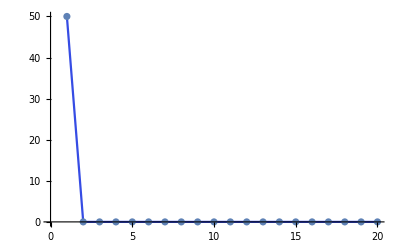

```mathematica
Listplott0=ListPlot[Told,ColorFunction->"TemperatureMap",Axes->True,FrameTicks->Automatic, Joined->True, Mesh->All]
```

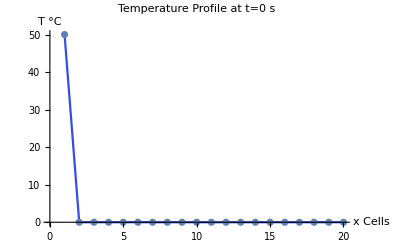

```mathematica
(* This shows the temperature profile at t=0 *)
Show[Listplott0,AxesLabel->{HoldForm[x Cells],HoldForm[T °C]},PlotLabel->HoldForm[Temperature Profile at t=0 s],LabelStyle->{GrayLevel[0]}]
```

```mathematica
(* This initalizes the new Temperature profile: *)
Tnew=Told;
(* This initializes the new Temperature profile in the form of a list: *)
TnewList={Told};
```

```mathematica
(* This calculates new temperature profile: *)
TnewLoop=Monitor[
(* First check if the Fourier number is still smaller than 0.1 *)
While[Tmax>t,
Do[
(*The formula for the Picard iteration is given in the book (see 3.3.8) *)
Tnew[[ii]]=(1-(2a*Δt)/Δx^2)Told[[ii]]+(a*Δt)/Δx^2(Told[[ii-1]]+Told[[ii+1]]),{ii, 2, n-1}];
(* This calculates the new value for time: *)
t=t+Δt;
(* This replaces the old profile with the new profile: *)
Told=Tnew;
(*The new temperature profile is added to the list so that we can later on find the temperature profile at each time interval *)
AppendTo[TnewList, Tnew];
];
,ProgressIndicator[Dynamic[1/Tmax],{0,1/Δt}]];
```

```mathematica
(* The new values of the temperature profile at t ≅ 980 s *)
Tnew
```

{50,47.3664,44.7328,42.0993,39.4661,36.833,34.2001,31.5676,28.9353,26.3034,23.6718,21.0406,18.4097,15.7791,13.1488,10.5187,7.88882,5.25912,2.62953,0}

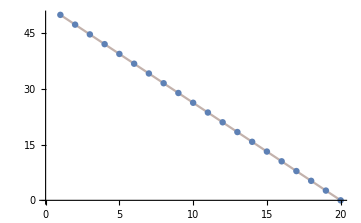

```mathematica
ListPlottmax=ListPlot[Tnew,ColorFunction->"TemperatureMap",Axes->True,FrameTicks->Automatic, Joined->True, Mesh->All]
```

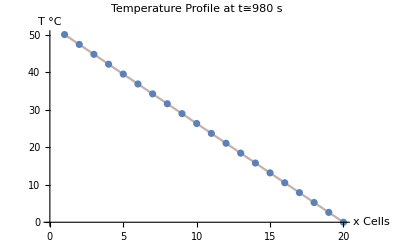

```mathematica
(* This shows the temperature profile at t=980s*)
Show[ListPlottmax,AxesLabel->{HoldForm[x Cells],HoldForm[T °C]},PlotLabel->HoldForm[Temperature Profile at t≅980 s],LabelStyle->{GrayLevel[0]}]
```

```mathematica
(* This shows the temperature profile at each time interval. Please note, that you have to enable dynamics and run the whole notebook before it works. *)
Manipulate[
ListPlot[TnewList[[tt]],ColorFunction->"TemperatureMap",Axes->True,FrameTicks->Automatic, Joined->True, Mesh->All]
,{tt,1,Length[TnewList]}]
```